## Ecuaciones Diferenciales CE51 - 16i

# Tarea B

Instrucciones:  Estudiar los temas discutidos en este documento.  Realizar las actividades en Wolfram-Mathematica indicadas en fondo rosa.  Realizar las actividades a lápiz y papel indicadas en fondo morado.

Notas:  
a)  Para los problemas a resolver a lápiz y papel, lo que más se tomará en cuenta para su calificación es la explicación del procedimiento.  Para resolver pasos individuales del desarrollo se permite el uso de la computadora siempre y cuando su uso se clarifique en la redacción del procedimiento.
b)  Las soluciones a lápiz y papel se entregan individidualmente (al igual que el desarrollo en Wolfram-Mathematica).

## Diálisis de riñón

El principal propósito del riñón es remover productos de desecho de la sangre, como la urea y la creatinina.  Cuando los riñones no trabajan apropiadamente, los desechos se acumulan en la sangre; cuando éstos alcanzan niveles tóxicos se produce la muerte.  Las principales causas de disfunción crónica de los riñones es la hipertensión y la diabetes mellitus.  Afortunadamente, el procedimiento de hemodiálisis de riñón remueve los productos de desecho de la sangre de pacientes con disfunción renal.  Durante éste proceso, la sangre del paciente se bombea atravez del dializador, usualmente a una tasa de 1 a 3 decilitros por minuto.  La sangre del paciente se separa de un “fluído limpiador” mediante una membrana semipermeable, la cual permite el paso de los desechos (pero no de las células de sangre) para ser diluídos en el líquido limpiador; éste a su vez contiene algunas sustancias benéficas para el cuerpo las cuales se diluyen en la sangre.  El “líquido limpiador”, que se conoce como dialisato, fluye en dirección opuesta a la sangre, usualmente a una tasa de 2 a 6 decilitros por minuto.  Los productos de desecho de la sangre se diluyen hacia el dialisato atravez de la membrana a una tasa proporcional a la diferencia de concentración entre los productos de desecho en la sangre y el dialisato.   Sea u(x) la concentración de desechos en la sangre y v(x) la concentración de desechos en el dialisato, donde x es la distancia a lo largo del dializador.  Entonces

{       Q_B u'==-k(u-v)
-Q_Dv'==k(u-v)

donde Q_D representa la tasa de flujo del dialisato atravez de la máquina, Q_B la tasa de flujo de la sangre atravez de la máquina, y k es una constante de proporcionalidad.

### Desarrollo en Wolfram-Mathematica

Sea L la longitud del dializador, sea u(0)=u_0 la concentración inicial de desechos en la sangre, y sea v(L)=0 la consentración inicial de desechos en el dialisato.  Entonces debemos resolver el problema de condiciones iniciales:

{        Q_B u'==-k(u-v)
-Q_Dv'==k(u-v)
    u(0)==u_0, v(L)==0

Use el comando DSolve para resolver este problema de condiciones iniciales.

```mathematica
sol1 =DSolve[{qqb u'[x]==-k(u[x]-v[x]),-qqd v'[x]==k(u[x]-v[x]),u[0]==u0,v[ll]==0},{u[x],v[x]},x]
```

{{u[x]→((ⅇ^((k ll (qqb-qqd))/(qqb qqd)) qqb-ⅇ^((k (qqb-qqd) x)/(qqb qqd)) qqd) u0)/(ⅇ^((k ll (qqb-qqd))/(qqb qqd)) qqb-qqd),v[x]→-((-ⅇ^((k ll (qqb-qqd))/(qqb qqd))+ⅇ^((k (qqb-qqd) x)/(qqb qqd))) qqb u0)/(ⅇ^((k ll (qqb-qqd))/(qqb qqd)) qqb-qqd)}}

```mathematica
Clear [ux,vx,k ,ll,qqb,qqd,u0];
```

```mathematica
ux = sol1[[1,1,2]]
```

((ⅇ^((k ll (qqb-qqd))/(qqb qqd)) qqb-ⅇ^((k (qqb-qqd) x)/(qqb qqd)) qqd) u0)/(ⅇ^((k ll (qqb-qqd))/(qqb qqd)) qqb-qqd)

```mathematica
vx = sol1[[1,2,2]]
```

-((-ⅇ^((k ll (qqb-qqd))/(qqb qqd))+ⅇ^((k (qqb-qqd) x)/(qqb qqd))) qqb u0)/(ⅇ^((k ll (qqb-qqd))/(qqb qqd)) qqb-qqd)

Para un adulto sano los niveles típicos de urea (contenido de nitrógeno) son entre 11 y 23 miligramos por decilitro, mientras que los niveles de creatinina varian entre 0.6 y 1.2 miligramos por decilitro.  (Considere que la concentración u(x) de desechos en sangre es la suma las concentraciones de urea y creatinina).  El volumen total de sangre es de 4 a 5 litros.

Supongamos que la hemodiálisis se efectúa en un paciente con niveles de urea de 34 mg/dl y de creatinina de 1.8 mg/dl, usando un dializador con k=2.25 y L=1.  La tasa de flujo de la sangre es Q_B=2 dl/min y la tasa de flujo del dialistato es Q_D=4 dl/min.

Grafique u[x] y v[x] sobre el intervalo [0,1].

```mathematica
k= 2.2;
ll=1;
qqb=2;
qqd=4;
u0=34;
```

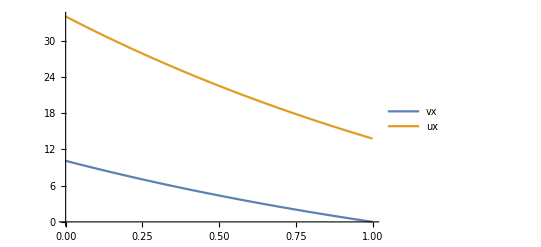

```mathematica
Plot[{vx,ux},{x,0,1},PlotLegends->"Expressions"]
```

Conteste la pregunta:  ¿se alcanzan los niveles normales de desechos en sangre después de que se efectúa la diálisis?

El nivel maximo de desechos en la sangre es de 24.2 por lo que en el punto donde x es igual a 1 u[x] es menor a esa cantidad por lo cual si se alcanzan los niveles normales de desecho.

### Desarrollo a lápiz y papel

Resuelva a mano el problema de condiciones iniciales (DisplayFormulaNumbered).

Sugerencia:
     i)  Sea y=u-v.  Muestre que y satisface la ecuación diferencial y'==-α y, donde α=k/Q_B-k/Q_D.
     ii)  Resuelva dicha ecuación diferencial.  (Esto debe ser fácil para usted.)
     iii)  Ahora que ya conoce usted quién es y(x), use la primera ecuación en (Title) y v=u-y para encontrar la ecuación u'(x)==f(x) que define a u.  Resuélvala.  Luego determine la expresión para v.
     iv)  Use las condiciones iniciales para determinar las constantes de integración.

## Modelo de persecución

Suponga que un objeto persigue a otro cuyo movimiento se conoce en virtud de alguna estrategia predeterminada.  Por ejemplo, piense en un avión con posición inicial en B(1000,0) que vuela hacia otro aeropuerto en A(0,0), es decir, que está 1000 kilómetros directamente al oeste de B, como se muestra en la figura Title.  Asumamos que el avión apunta hacia A todo el tiempo.  Si el viento sopla de sur a norte a velocidad constante w, y la rapidez del avión en aire quieto es b, nos planteamos el problema de determinar la condición sobre b para que el avión eventualmente llegue a A y la descripción de la trayectoria.

-Graphics-

▲ Figura outputGraphics

### Desarrollo en Wolfram-Mathematica

De acuerdo a lo descrito, la rapidez del avión b debe ser mayor que la velocidad del viento w.  Note que dx/dt describe la componente x de la velocidad del avión, por lo que

ⅆx/ⅆt=-b  cos θ=(-b x)/(√(x^2+y^2))

toda vez que, por trigonometría elemental, cos θ=x/√(x^2+y^2).  Análogamente,

ⅆy/ⅆt=-b  sen θ+w=(-b y)/(√(x^2+y^2))+w ,

por lo que

ⅆy/ⅆt=(ⅆy/ⅆt)/(ⅆx/ⅆt)=((-b y)/(√(x^2+y^2))+w)/((-b x)/(√(x^2+y^2)))=(b y - w √(x^2+y^2))/(b x) .

Ésta es una ecuación homogénea (de grado uno) puesto que se puede escribir de la forma ⅆy/ⅆx=F(y/x) :

ⅆy/ⅆx=(b y - w √(x^2+y^2))/(b x)=y/x-w/b √(1+(y/x)^2) .

Así, debemos resolver el problema de valores iniciales:

{ⅆy/ⅆx==(b y-w √(x^2+y^2))/(b x)
y(1000)==0

Use el comando DSolve para resolver este problema de valores iniciales.

```mathematica
sol2=DSolve[{y'[x]==(b y[x]-w(Sqrt[(x^2+y[x]^2)]))/(b x),y[1000]==0},{y[x]},x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→x Sinh[(w Log[1000]-w Log[x])/b]}}

Use el comando Plot para graficar y(x) sobre el intervalo x∈[0,1000].  Para ello fije b=1 y use el comando Table para generar las funciones y[x] correspondientes a w=0.25,0.50,…,2.0.  (Note que el avión nunca llega a A si w/b≥1.)

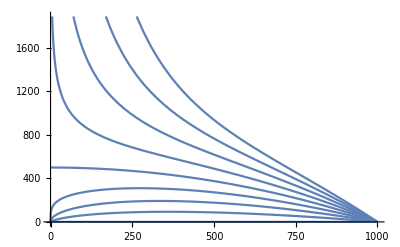

```mathematica
Plot[Table[sol2[[1,1,2]],{w,0,2.0,.25}]/.{b->1},{x,0,1000}]
```

### Desarrollo a lápiz y papel

Nos proponemos ahora resolver a mano el problema de valores iniciales (DisplayFormulaNumbered).

Sea y=u x.  Diferenciando se obtiene que ⅆy==u ⅆx+x ⅆu.  Sustituyendo en la primera ecuación en (DisplayFormulaNumbered) y simplificando, demuestre que

1/(√(1+u^2))ⅆu==-w/b 1/x ⅆx

Resuelva esta ecuación diferencial, usando la condición inicial para determinar la constante de integración.

Resubstituya u=y/x para despejar y y obtener la solución de (DisplayFormulaNumbered).